# SIESTA

## Mark Cianciosa 8/1/2019

This plots out poincare plots from a siesta restart file.

## Stellarator Asymmetric Case

## File Open

Load the SIESTA restart file.

```mathematica
restartfile=SystemDialogInput["FileOpen"]
```

### SIESTA Quantities

Load physical quantities from the restart file.

```mathematica
bsupsmns=Normal[Import[restartfile,{"Datasets","JBsupssh_m_n_r_"}]];
bsupumnc=Normal[Import[restartfile,{"Datasets","JBsupuch_m_n_r_"}]];
bsupvmnc=Normal[Import[restartfile,{"Datasets","JBsupvch_m_n_r_"}]];
```

```mathematica
rmnc=Normal[Import[restartfile,{"Datasets","rmnc_m_n_r_"}]];
zmns=Normal[Import[restartfile,{"Datasets","zmns_m_n_r_"}]];
```

```mathematica
mpol=Import[restartfile,{"Datasets","mpol"}];
ntor=Import[restartfile,{"Datasets","ntor"}];
```

```mathematica
nrad=Import[restartfile,{"Datasets","nrad"}];
```

```mathematica
nfp=Import[restartfile,{"Datasets","nfp"}];
```

## Radial Interpolation

Interpolate the radial grids.

### Radial Grids

Radial grid for the full and half grid quantities.

```mathematica
sSIESTAF=Subdivide[0,1,nrad-1];
sSIESTAH=(sSIESTAF[[;;-2]]+sSIESTAF[[2;;]])/2;
```

### Interpolation Functions

Interpolate over entire positive to negative points to obtain the correct derivatives at the magnetic axis. Even m modes Fourier amplitudes will have the same parity. Odd modes Fourier amplitudes will have opposite parity.

#### SIESTA Functions

Half grid functions

```mathematica
bsupsmnsInt=ParallelTable[Interpolation[Join[Transpose[{Reverse[-sSIESTAH],Reverse[If[Mod[m,2]==0,1,-1]*bsupsmns[[2;;,n+ntor+1,m+1]]]}],Transpose[{sSIESTAH,bsupsmns[[2;;,n+ntor+1,m+1]]}]],InterpolationOrder->10],{n,-ntor,ntor,1},{m,0,mpol,1}];
bsupumncInt=ParallelTable[Interpolation[Join[Transpose[{Reverse[-sSIESTAH],Reverse[If[Mod[m,2]==0,1,-1]*bsupumnc[[2;;,n+ntor+1,m+1]]]}],Transpose[{sSIESTAH,bsupumnc[[2;;,n+ntor+1,m+1]]}]],InterpolationOrder->10],{n,-ntor,ntor,1},{m,0,mpol,1}];
bsupvmncInt=ParallelTable[Interpolation[Join[Transpose[{Reverse[-sSIESTAH],Reverse[If[Mod[m,2]==0,1,-1]*bsupvmnc[[2;;,n+ntor+1,m+1]]]}],Transpose[{sSIESTAH,bsupvmnc[[2;;,n+ntor+1,m+1]]}]],InterpolationOrder->10],{n,-ntor,ntor,1},{m,0,mpol,1}];
```

Full grid functions

```mathematica
rmncInt=ParallelTable[Interpolation[Join[Transpose[{Reverse[-sSIESTAF[[2;;]]],Reverse[If[Mod[m,2]==0,1,-1]*rmnc[[2;;,n+ntor+1,m+1]]]}],Transpose[{sSIESTAF,rmnc[[;;,n+ntor+1,m+1]]}]],InterpolationOrder->10],{n,-ntor,ntor,1},{m,0,mpol,1}];
zmnsInt=ParallelTable[Interpolation[Join[Transpose[{Reverse[-sSIESTAF[[2;;]]],Reverse[If[Mod[m,2]==0,1,-1]*zmns[[2;;,n+ntor+1,m+1]]]}],Transpose[{sSIESTAF,zmns[[;;,n+ntor+1,m+1]]}]],InterpolationOrder->10],{n,-ntor,ntor,1},{m,0,mpol,1}];
```

```mathematica
rmnclcfs=rmnc[[100]];
zmnslcfs=zmns[[100]];
```

## Inverse Fourier Transform

Transform Fourier representation to real space.

### SIESTA Transform

SIESTA Functions take the following form depending on the parity.

A(s,u,v)=∑_m ∑_n A_mnc(s)cos(m*u+nfp*n*v)

```mathematica
bsups[s_,u_,v_]:=Evaluate[Sum[bsupsmnsInt[[n+ntor+1,m+1]][s]*Sin[m*u+nfp*n*v],{m,0,mpol,1},{n,-ntor,ntor,1}]];
bsupu[s_,u_,v_]:=Evaluate[Sum[bsupumncInt[[n+ntor+1,m+1]][s]*Cos[m*u+nfp*n*v],{m,0,mpol,1},{n,-ntor,ntor,1}]];
bsupv[s_,u_,v_]:=Evaluate[Sum[bsupvmncInt[[n+ntor+1,m+1]][s]*Cos[m*u+nfp*n*v],{m,0,mpol,1},{n,-ntor,ntor,1}]];
```

```mathematica
rsuv[s_,u_,v_]:=Evaluate[Sum[rmncInt[[n+ntor+1,m+1]][s]*Cos[m*u+nfp*n*v],{m,0,mpol,1},{n,-ntor,ntor,1}]];
zsuv[s_,u_,v_]:=Evaluate[Sum[zmnsInt[[n+ntor+1,m+1]][s]*Sin[m*u+nfp*n*v],{m,0,mpol,1},{n,-ntor,ntor,1}]];
```

```mathematica
rlcfs[u_,v_]:=Sum[rmnclcfs[[n+ntor+1,m+1]]*Cos[m*u+nfp*n*v],{m,0,mpol,1},{n,-ntor,ntor,1}];
zlcfs[u_,v_]:=Sum[zmnslcfs[[n+ntor+1,m+1]]*Sin[m*u+nfp*n*v],{m,0,mpol,1},{n,-ntor,ntor,1}];
```

## Field Line Following

```mathematica
fieldLine[s0_,u0_,v0_,vend_]:=ParallelMap[
Reap[
If[v0==0,Sow[{{#,Mod[u0,2Pi]},{r[#,u0,0],z[#,u0,0]}},a]];
NDSolve[
{s'[v]==bsups[s[v],u[v],v]/bsupv[s[v],u[v],v],
u'[v]==bsupu[s[v],u[v],v]/bsupv[s[v],u[v],v],
s[0]==#,u[0]==u0,
WhenEvent[Sin[v*nfp]==Sin[0.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},aa],Null]],
WhenEvent[Sin[v*nfp]==Sin[9.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},bb],Null]],
WhenEvent[Sin[v*nfp]==Sin[18.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},cc],Null]],
WhenEvent[Sin[v*nfp]==Sin[27.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},dd],Null]],
WhenEvent[Sin[v*nfp]==Sin[36.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ee],Null]],
WhenEvent[Sin[v*nfp]==Sin[45.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ff],Null]],
WhenEvent[Sin[v*nfp]==Sin[54.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},gg],Null]],
WhenEvent[Sin[v*nfp]==Sin[63.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},hh],Null]],
WhenEvent[Sin[v*nfp]==Sin[72.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ii],Null]],
WhenEvent[Sin[v*nfp]==Sin[81.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},jj],Null]],
WhenEvent[Cos[v*nfp]==Cos[90.0*Pi/180.0],If[Sin[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},kk],Null]],
WhenEvent[Sin[v*nfp]==Sin[99.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ll],Null]],
WhenEvent[Sin[v*nfp]==Sin[108.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},mm],Null]],
WhenEvent[Sin[v*nfp]==Sin[117.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},nn],Null]],
WhenEvent[Sin[v*nfp]==Sin[126.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},oo],Null]],
WhenEvent[Sin[v*nfp]==Sin[135.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},pp],Null]],
WhenEvent[Sin[v*nfp]==Sin[144.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},qq],Null]],
WhenEvent[Sin[v*nfp]==Sin[153.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},rr],Null]],
WhenEvent[Sin[v*nfp]==Sin[162.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ss],Null]],
WhenEvent[Sin[v*nfp]==Sin[171.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},tt],Null]],
WhenEvent[Sin[v*nfp]==Sin[180.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},uu],Null]],
WhenEvent[Sin[v*nfp]==Sin[189.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},vv],Null]],
WhenEvent[Sin[v*nfp]==Sin[198.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ww],Null]],
WhenEvent[Sin[v*nfp]==Sin[207.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},xx],Null]],
WhenEvent[Sin[v*nfp]==Sin[216.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},yy],Null]],
WhenEvent[Sin[v*nfp]==Sin[225.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},zz],Null]],
WhenEvent[Sin[v*nfp]==Sin[234.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},aaa],Null]],
WhenEvent[Sin[v*nfp]==Sin[245.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},bbb],Null]],
WhenEvent[Sin[v*nfp]==Sin[252.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ccc],Null]],
WhenEvent[Sin[v*nfp]==Sin[261.0*Pi/180.0],If[Cos[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ddd],Null]],
WhenEvent[Cos[v*nfp]==Cos[270.0*Pi/180.0],If[Sin[v*nfp]<0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},eee],Null]],
WhenEvent[Sin[v*nfp]==Sin[279.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},fff],Null]],
WhenEvent[Sin[v*nfp]==Sin[288.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},ggg],Null]],
WhenEvent[Sin[v*nfp]==Sin[297.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},hhh],Null]],
WhenEvent[Sin[v*nfp]==Sin[306.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},iii],Null]],
WhenEvent[Sin[v*nfp]==Sin[315.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},jjj],Null]],
WhenEvent[Sin[v*nfp]==Sin[324.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},kkk],Null]],
WhenEvent[Sin[v*nfp]==Sin[333.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},lll],Null]],
WhenEvent[Sin[v*nfp]==Sin[342.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},mmm],Null]],
WhenEvent[Sin[v*nfp]==Sin[351.0*Pi/180.0],If[Cos[v*nfp]>0,Sow[{{s[v],Mod[u[v],2Pi]},{rsuv[s[v],u[v],v],zsuv[s[v],u[v],v]}},nnn],Null]]
},{s,u},{v,v0,vend},Method->{"EquationSimplification"->"Residual"}
],{aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx,yy,zz,aaa,bbb,ccc,ddd,eee,fff,ggg,hhh,iii,jjj,kkk,lll,mmm,nnn}
]&,s0,Method->"FinestGrained"]
```

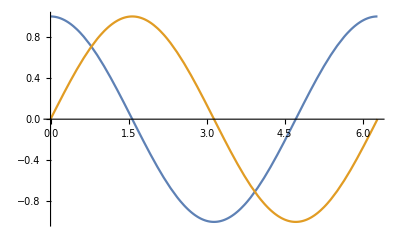

```mathematica
Plot[{Cos[v],Sin[v]},{v,0,2Pi}]
```

```mathematica
poincare=fieldLine[Subdivide[0.0,1.0,nrad-1],0,0,1000*2*Pi/nfp];
```

```mathematica
surfaces=ParametricPlot[Evaluate[ParallelMap[{rsuv[#,u,0],zsuv[#,u,0]}&,Subdivide[0,1,10]]],{u,0,2Pi},PlotStyle->Black,Frame->True,BaseStyle->Directive[36,Black,FontFamily->"Times"],FrameStyle->Directive[24,Black,FontFamily->"Times"],ImageSize->Large]
```

```mathematica
usurfaces=ParametricPlot[Evaluate[ParallelMap[{rsuv[s,#,0],zsuv[s,#,0]}&,Subdivide[0,2Pi,13]]],{s,0,1},PlotStyle->Black]
```

```mathematica
Show[Graphics[Black],surfaces,usurfaces]
```

```mathematica
Show[
surfaces,
ListPlot[poincare[[;;,2,1,1,;;,2]],AspectRatio->Automatic,ImageSize->Large,Epilog->Text["ϕ,=,"<>ToString[(1-1)*30]Degree,{1.9,1.2},BaseStyle->Directive[36,Black,FontFamily->"Times"]],FrameStyle->Directive[24,Black,FontFamily->"Times"]]
]
```

```mathematica
Show[
ListPlot[poincare[[;;,2,1,1,;;,2]],Frame->True,AspectRatio->Automatic,Epilog->Text["ϕ="<>ToString[(1-1)*9.0/nfp]Degree,{4.75,0.8},BaseStyle->Directive[18,Black]],FrameStyle->Directive[18,Black],FrameLabel->{"R (m)","Z (m)"}],surfaces
]
```

```mathematica
movie=ParallelTable[Show[
ListPlot[poincare[[;;,2,i,1,;;,2]],Frame->True,AspectRatio->1,PlotRange->{{0.5,1.0},{-0.25,0.25}},ImageSize->{8*72,8*72},Epilog->Text["ϕ="<>ToString[(i-1)*9.0/nfp]Degree,{0.9,0.2},BaseStyle->Directive[36,Black,FontFamily->"Times"]],FrameStyle->Directive[24,Black,FontFamily->"Times"]],
ParametricPlot[{rlcfs[u,(i-1)*9.0/nfp*Pi/180],zlcfs[u,(i-1)*9.0/nfp*Pi/180]},{u,0,2Pi},PlotStyle->Directive[Thick,Black,Dashed]]
],{i,Length[poincare[[1,2,;;]]]}]
```

```mathematica
Export["3DSimple.gif",movie,"DisplayDurations"->0.1,"AnimationRepetitions"->∞]
```

```mathematica
Export["test.mp4",movie,"FrameRate"->4,"VideoEncoding"->"H264-AVF"]
```

## Q Profile

```mathematica
woutfile=SystemDialogInput["FileOpen"]
```

```mathematica
ns=Import[woutfile,{"Datasets","ns"}];
qfactor=Normal[Import[woutfile,{"Datasets","q_factor"}]];
```

```mathematica
svmec=Subdivide[0,1,ns-1];
sSiestaVMEC=Sqrt[svmec];
```

```mathematica
iota[i_]:=Integrate[u[v]/.poincare[[i,1,1,2]],{v,0,1000*2*Pi/nfp}]/Integrate[v,{v,0,1000*2*Pi/nfp}];
```

```mathematica
Show[
ListLinePlot[{ParallelTable[{sSIESTAF[[i]],1.0/iota[i]},{i,1,Length[sSIESTAF],1}],Transpose[{sSiestaVMEC,qfactor}]},Frame->True,FrameLabel->{"s","q"},PlotStyle->{Red,Blue},LabelStyle->Directive[18,Black],PlotRange->{{0,1},Full},PlotLegends->{"SIESTA","VMEC"}],
Graphics[{Black,Dashed,Line[{{0.0,1.0},{1.0,1.0}}]}],
Graphics[{Black,Dashed,Line[{{0.0,2.0},{1.0,2.0}}]}],
Graphics[{Black,Dashed,Line[{{0.0,3.0},{1.0,3.0}}]}]
]
```